# 2. domača naloga 2025/26 - 1.del

## 1. naloga

a) Izračunajte neskončno vsoto 1+1/9+1/25+1/49+1/81+...
b) Izračunajte limito funkcije 
		f(x) = (sin(x)-x)/x^3,
    ko gre x proti 0.
c) Izračunajte ploščino lika, ki ga omejujejo graf funkcije g(x) = sin(x)+x^2, abscisna os ter navpičnici x=0 in x=2π.
d) Izračunajte ploščino lika, ki ga omejujeta grafa funkcij g(x) = sin(x)+x^2 in g1(x) = sin(x) + x^5/5.

```mathematica
Sum[1/(2 n+1)^2,{n,0,Infinity}]
```

π^2/8

```mathematica
Limit[(Sin[x]-x)/x^3,x->0]
```

-1/6

```mathematica
Integrate[Sin[x]+x^2,{x,0,2 Pi}]
```

(8 π^3)/3

```mathematica
g[x_]:=Sin[x]+x^2
g1[x_]:=Sin[x]+x^5/5
Solve[g[x]==g1[x],x]
Integrate[g[x]-g1[x],{x,0,5^(1/3)}]
```

{{x→0},{x→0},{x→-(-5)^(1/3)},{x→5^(1/3)},{x→(-1)^(2/3) 5^(1/3)}}

5/6

## 2. naloga

a)  Definirajte funkcijo A(m,n), ki sprejme naravni števili  in  in vrne matriko dimenzije , kjer se na vsakem mestu v matriki pojavi vsota indeksa stolpca in indeksa vrstice.
b) Izračunajte determinanto, rang in lastne vrednosti matrike . Kaj opazite?
c)  Narišite vektorje, ki ustrezajo stolpcem matrike . S pomočjo ukaza InfinitePlane na sliko narišite še ravnino, v kateri ti trije vektorji ležijo. 
d) Določite parametra, s katerima lahko prvi stolpec matrike A(3,3) izrazimo z drugima dvema.
e) Določite cela števila α, x_1,x_2 in x_3, ki zadoščajo enakosti 
		M (x_1
x_2
x_3) = (-3
-5
-9
-11) ,
    kjer je M matrika, podana kot A(4,3)+αI, kjer I označuje identično matriko ustrezne velikosti. Rešitev zapišite v eni vrstici.

```mathematica
A[m_,n_]:=Table[i+j,{i,n},{j,m}]
```

```mathematica
mat=A[3,3]
Det[mat]
MatrixRank[mat]
Eigenvalues[mat]
```

{{2,3,4},{3,4,5},{4,5,6}}

0

2

{6+√42,6-√42,0}

```mathematica
v1={2,3,4};
v2={3,4,5};
v3={4,5,6};

Graphics3D[{Arrow[{{0,0,0},v1}],Arrow[{{0,0,0},v2}],Arrow[{{0,0,0},v3}],InfinitePlane[{v1,v2,v3}]}]
```

-Graphics3D-

```mathematica
v1={2,3,4};
v2={3,4,5};
v3={4,5,6};

Solve[v1==a v2+b v3,{a,b}]
```

{{a→2,b→-1}}

```mathematica
M=A[3,3]+α IdentityMatrix[3];

Solve[M.{x1,x2,x3}=={-3,-5,-9},{α,x1,x2,x3},Integers]
```

{{α→-2,x1→-1,x2→-1,x3→0}}

## 3. naloga

V datoteki ‘vreme.xlsx’ se nahajajo podatki o najvišjih in povprečnih mesečnih temperaturah v Ljubljani v letu 2025. Podatke uvozite v Mathematico.

a) Grafično predstavite podatke o najvišjih mesečnih temperaturah (graf naj bo čim bolj podoben spodnjemu). Pri tem vrednosti temperatur in številke mesecev z ustreznimi poizvedbami preberite iz uvožene tabele.
b) Napišite poizvedbo, ki bo vrnila imena ‘toplih mesecev’ - to so tisti meseci, katerih povprečna temperatura je višja ob 15 stopinj. Poizvedbo poskusite napisati v eni vrstici.

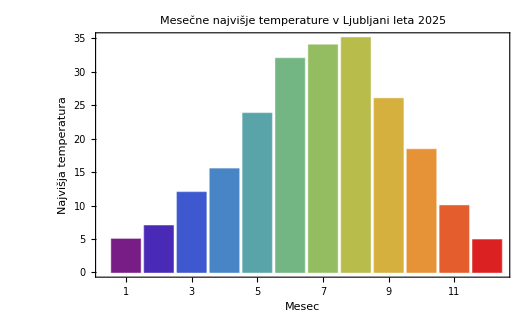

```mathematica
podatki=Import[SystemDialogInput["FileOpen"]]
```

{{{Številka,Mesec,Najvišja,Povprečna},{1.,Januar,5.,2.5},{2.,Februar,7.,2.},{3.,Marec,12.,8.},{4.,April,15.5,12.2},{5.,Maj,23.8,15.3},{6.,Junij,32.,22.9},{7.,Julij,34.,21.8},{8.,Avgust,35.1,21.6},{9.,September,26.,17.4},{10.,Oktober,18.4,10.6},{11.,November,10.,6.6},{12.,December,4.9,3.7}}}

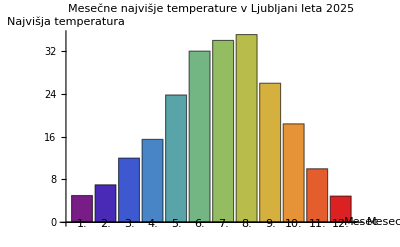

```mathematica
tabela=podatki[[1]];

meseci=tabela[[2;;,1]];
temp=tabela[[2;;,3]];

BarChart[temp,ChartLabels->meseci,AxesLabel->{"Mesec","Najvišja temperatura"},PlotLabel->"Mesečne najvišje temperature v Ljubljani leta 2025",ChartStyle->"Rainbow"]
```

```mathematica
Cases[tabela[[2;;]],{_,mesec_,_,temp_}/;temp>15:>mesec]
```

{Maj,Junij,Julij,Avgust,September}